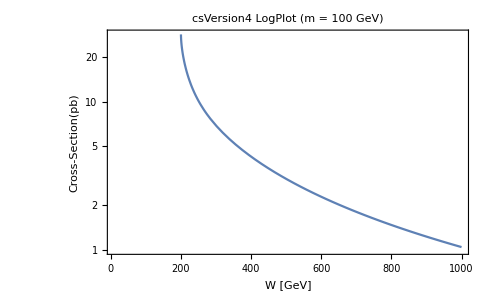

```mathematica
mtau=100.0;
hbarc2=0.389;
alpha2=(1.0/133.0)*(1.0/133.0);

beta=If[1.0-4.0*mtau*mtau/W^2>=0,Sqrt[1.0-4.0*mtau*mtau/W^2],Indeterminate];

LogPlot[4.0*Pi*hbarc2*alpha2/W^2*(2.0*(1.0+4.0*mtau^2.0/W^2-8.0*mtau^4.0/W^4.0)*Log[2.0*W/(mtau*(1.0+beta))]-beta*(1.0+4.0*mtau^2.0/W^2))*10^9,{W,100,1000},FrameLabel->{"W [GeV]","Cross-Section(pb)"},PlotLabel->"csVersion4 LogPlot  (m = 100 GeV)",Frame->True,GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->{{10,1000},{1,Automatic}}]
```